```mathematica
(* Solving Newton's equations ddotx == 0, ddoty = -g gives *)
```

```mathematica
v0 = 20; g =9.81;
x[t_,θ_]:=Module[{},
t v0 Cos[θ]
]
y[t_,θ_]:=Module[{},
-g t^2/2 + v0 Sin[θ] t + 100
]
(* Time where the parabola hits the ground. *)
tint[θ_]:=Module[{},
(2 v0 Sin[θ]+√(800 g+4 v0^2 Sin[θ]^2))/(2 g)
]
```

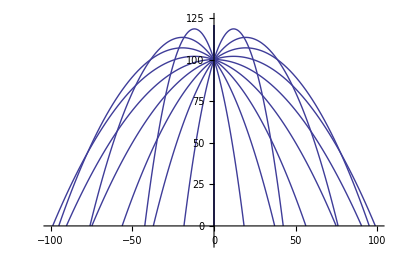

```mathematica
(* Make a plot of falling fireworks fragements *)
nm=10;
thvl=Pi Range[-nm,nm]/nm+Pi/2;
Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

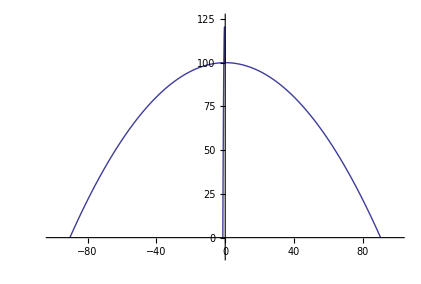

```mathematica
(* Plot of the fragments that have horizontal velocity vecs (and are the furthest from the point where the initial explosino occurred ) *)
nm=10;
thvl={0,Pi,Pi/2+0.01};
Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

```mathematica
(* Find the area under the base curve first using standard calculus.  Then find the lengths of the curves with θ between 0 and Pi from t = 0 until the intersect either the left or right curve.  Integrate over these arc lengths to find the upper area.  Finally find the area of the region by usuing rotation. s*)
```

```mathematica
bsecrv = {x[t,0],y[t,0]}
```

{20 t,100-4.905 t^2}

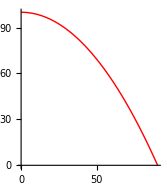

```mathematica
(* Do this for θ from 0 to Pi/2 .. note we only need half by symmetry. *)
g1=ParametricPlot[bsecrv,{t,0,tint[0]},PlotStyle->Red]
```

```mathematica
eqn={x[t,θ1],y[t,θ1]}-bsecrv
```

{-20 t+20 t Cos[θ1],0.+20 t Sin[θ1]}

```mathematica
crvint[θ_]:=(Cos[θ]-1)
```

```mathematica
θvls=Pi/2 Range[0,nm]/nm +Pi;
gr= Table[0,{i,1,Length[θvls]}];
For[i=1,i≤Length[gr],++i,
θvlstmp = θvls[[i]];
gr[[i]]=ParametricPlot[{x[t,θvlstmp],y[t,θvlstmp]},{t,0,crvint[θvlstmp]},PlotRange->{{0,60},{0,140}}];
]
```

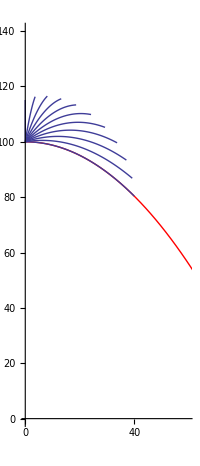

```mathematica
g1=ParametricPlot[bsecrv,{t,0,tint[0]},PlotStyle->Red,PlotRange->{{0,60},{0,140}}];
g2=Show[gr,PlotRange->{{0,60},{0,140}}];
Show[g1,g2]
```

```mathematica
(* Do this for θ from 0 to Pi/2 *)
```

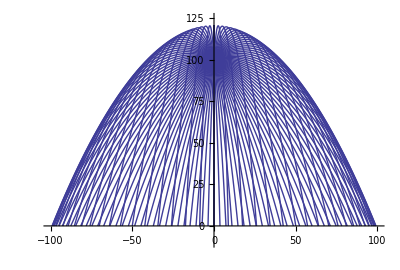

```mathematica
(* Another idea *) 
(* The envelope of the trajectories is traced out by the max of the y-values of the projectiles that vary over different θ values, as can be seen in the picture below.  Let's construct this function. *)
nm=50;
thvl=Pi Range[-nm,nm]/nm+Pi/2;
g1=Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

```mathematica
xfun[θ_]:=40.77471967380224 Cos[θ] Sin[θ]
maxfun[θ_]:=100+20.38735983690112 Sin[θ]^2
```

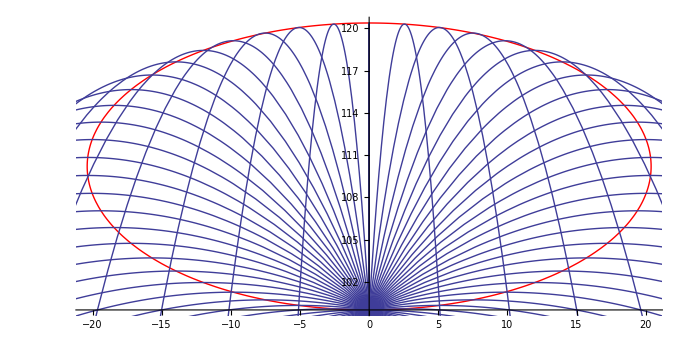

```mathematica
g2=ParametricPlot[{xfun[t],maxfun[t]},{t,0, Pi},PlotStyle->Red];
Show[g2,g1]
```

```mathematica
(* This shows that the max point is not the proper one to optimize! Instead let's try to optimize the max distance awa from our original point. *)
```

```mathematica
Clear[θ]
eqn=FullSimplify[D[x[t,θ]^2+(y[t,θ]-100)^2,t]];
sls=Solve[eqn==0,t];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
topt2[θ_]:=0.509683995922528 (1.4142135623730951 √(-7.-9. Cos[2. θ])+6. Sin[θ]);
topt3[θ_]:=0.509683995922528 (-1.4142135623730951 √(-7.-9. Cos[2. θ])+6. Sin[θ])
```

```mathematica
nm=10;
θ=Pi Range[0,nm]/nm+Pi/2;
g3=ParametricPlot[{x[topt2[θ],θ],y[topt2[θ],θ]},{θ,-Pi,Pi} ,PlotStyle->Red];
```

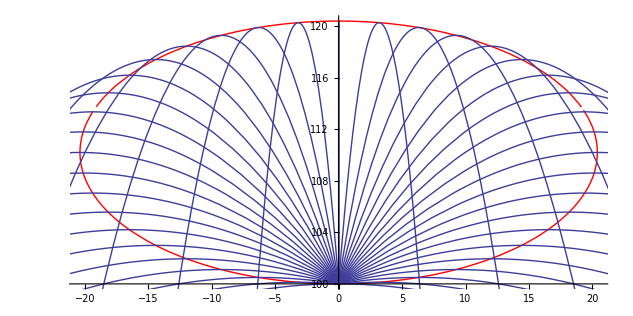

```mathematica
Show[g3,g1]
```

```mathematica
(* This idea is not going to work either! *)
```

```mathematica
121768-2299
```

119469

```mathematica
nm=20;
thvl=Pi Range[-nm,nm]/nm+Pi/2;
thvl2=Pi/2 Range[0,nm]/nm+Pi/4;
```

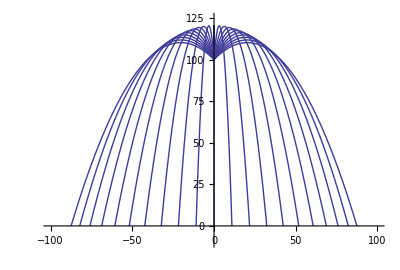

```mathematica
g1=Show[Table[ParametricPlot[{x[t,thvl2[[i]]],y[t,thvl2[[i]]]},{t,0,tint[thvl2[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl2]}],PlotRange->{{-100,100},{-10,125}}]
```

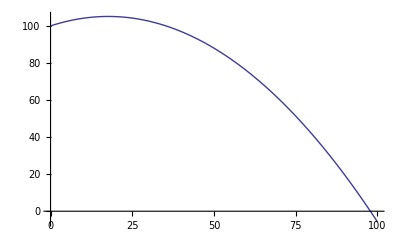

```mathematica
Plot[y[X/(20 Cos[θ]),θ]/.θ->Pi/6,{X,0,100}]
```

```mathematica
Solve[Simplify[(y[X/(20 Cos[θ+eps]),θ+eps]-y[X/(20 Cos[θ]),θ])/X]==0,X]
```

{{X→-(40 v0 Sec[θ] Sec[eps+θ] Sin[eps])/(g (Sec[θ]^2-Sec[eps+θ]^2))}}

```mathematica
Limit[-(40 v0 Sec[θ] Sec[eps+θ] Sin[eps])/(g (Sec[θ]^2-Sec[eps+θ]^2)),eps->0]
```

(20 v0 Cot[θ])/g

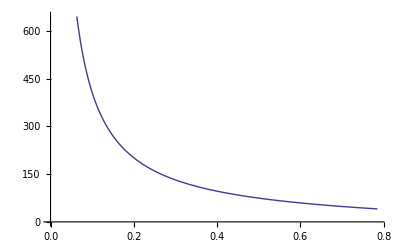

```mathematica
v0sub = 20; g = 9.81;
Plot[(20 v0 Cot[θ])/g/.{v0->20,g->9.81},{θ,0,Pi/4}]
```

```mathematica
Clear[g,v0]
Solve[x[t,θ]==20 v0 Cot[θ]/g,t]
```

{{t→(20 Csc[θ])/g}}

```mathematica
tsub=(20 Csc[θ])/g
```

2.03874 Csc[θ]

```mathematica
{x[tsub1,θ],y[tsub1,θ]}/.tsub1->20 Csc[θ]/gg
```

{(400 Cot[θ])/gg,100+400/gg-(1962. Csc[θ]^2)/gg^2}

```mathematica
g4=ParametricPlot[{x[tsub,θ],y[tsub,θ]}/.{v0->20,g->9.81},{θ,Pi/4,Pi/2},PlotStyle->Red];
```

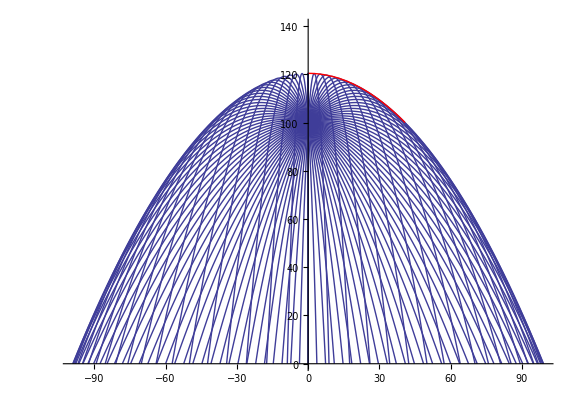

```mathematica
Show[g1,g4,PlotRange->{0,140}]
```

```mathematica
intvls={x[tsub1,θ],y[tsub1,θ]}/.tsub1->20 Csc[θ]/gg
```

{(400 Cot[θ])/gg,100+400/gg-(1962. Csc[θ]^2)/gg^2}

```mathematica
dydth=D[intvls[[2]],θ]
```

(3924. Cot[θ] Csc[θ]^2)/gg^2

```mathematica
area1=Integrate[Pi intvls[[1]] dydth,{θ,Pi/4,Pi/2}]
```

(1.64368×10^6)/gg^3

```mathematica
D[y[tsub,θ],θ]
```

40.7747 Cot[θ] Csc[θ]^2

```mathematica
Solst[[1]]
```

(20 v0 Cot[θ])/g

```mathematica
Solve[y[t,Pi/4]==0,t]
```

{{t→-3.29818},{t→6.18139}}

```mathematica
Simplify[Solve[-gg t^2/2 + v00 Sin[Pi/4] t + 100==0,t]]
```

{{t→(v00-√(400 gg+v00^2))/(√2 gg)},{t→(v00+√(400 gg+v00^2))/(√2 gg)}}

```mathematica
fint = (v00+√(400 gg+v00^2))/(√2 gg)/.{v00->20,gg->9.81};
```

6.18139

```mathematica
tsub=(20 Csc[θ])/gg
{x[tsub,θ],y[tsub,θ]}
```

(20 Csc[θ])/gg

{(400 Cot[θ])/gg,100+400/gg-(1962. Csc[θ]^2)/gg^2}